# Using Fourier Transforms for image compression

This code is based on:
https://demonstrations.wolfram.com/ImageCompressionViaTheFourierTransform/#popup1
by Chris Maes (March 2011)

### The idea

#### 1. Extracting image data

Here is an image:

```mathematica
img = ExampleData[{"TestImage","Lena"}]
```

-Graphics-

A colored image is described essentially by 3 matrices, denoting the intensity of Red, Green & Blue of each pixel (given as numbers between 0 and 1).

```mathematica
imgdata=ImageData[img]
```

{{{0.886275,0.537255,0.490196},{0.886275,0.537255,0.490196},{0.87451,0.537255,0.521569},{0.87451,0.533333,0.501961},504,{0.917647,0.584314,0.482353},{0.901961,0.580392,0.478431},{0.866667,0.509804,0.431373},{0.784314,0.388235,0.352941}},510,{1}}
 |  |  |  |

```mathematica
Dimensions[imgdata]
```

{512,512,3}

This means that the image is 512x512.

For simplicity we are going to make the images black and white, although the basic method also works perfectly fine for colors. 
To make it BW, we essentially take the average over the three colors.

```mathematica
imgBW = N@Map[1-Mean[#]&,imgdata,{2}]
```

{{0.362092,0.362092,0.355556,0.363399,0.36732,0.384314,0.360784,0.366013,0.354248,0.372549,0.360784,0.372549,0.397386,0.36732,0.375163,0.393464,0.394771,0.392157,0.371242,0.379085,0.4,0.398693,0.405229,0.393464,0.4,0.389542,0.397386,0.414379,457,0.470588,0.505882,0.487582,0.496732,0.511111,0.481046,0.498039,0.503268,0.482353,0.51634,0.503268,0.529412,0.512418,0.529412,0.512418,0.522876,0.529412,0.505882,0.499346,0.448366,0.354248,0.343791,0.341176,0.338562,0.346405,0.397386,0.491503},511}
 |  |  |  |

```mathematica
Dimensions[imgBW]
```

{512,512}

This is now just a single 512x512 matrix.

#### 2. Viewing the image data as a sequence

Let us look at one line of the image

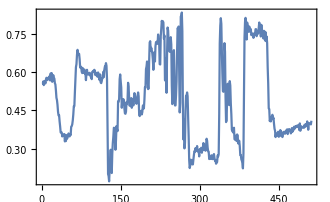

```mathematica
line = imgBW⟦200⟧;
ListLinePlot[line]
```

The color intensities varies along the image in a very irregular fashion. 
Just by looking at this plot does not reveal much about the image. 
For our brain to understand this, we need all lines of the matrix:

```mathematica
ArrayPlot[imgBW]
```

-Graphics-

#### 3. Spectral analysis of the image (Fourier Transform)

But, continuing to think about the single-line, we can now do a spectral analysis and see which frequencies occur more often.

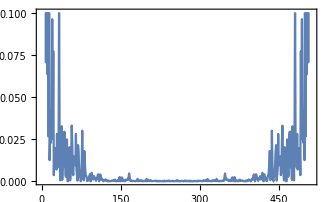

```mathematica
fftline = Fourier[line];
ListLinePlot[Abs[fftline]^2,PlotRange->{0,0.1}]
```

As can be seen, there is a lot of low frequency contributions, then a gap and then a lot of high frequencies: 

- Low frequencies mean features of the image which change slowly. 
- High frequencies mean features which change quickly. 

Now here comes the key idea: 
Our eye is not good at distinguishing rapidly changing features. Low frequency contributions matter much more to us.

This suggests that we can compress the image by:
- Go to Fourier space. 
- Chop off high frequency contributions. 
- Return to real space.

This chops (turns into 0) all elements of fftline which are smaller than 0.1

```mathematica
fftChop = Chop[fftline,10^-1]
```

{11.1931,-0.165897+0.270273 ⅈ,-0.260028-0.561209 ⅈ,-0.859701+1.22006 ⅈ,0.469539-0.283874 ⅈ,0.596803+0.19591 ⅈ,0.72841-0.359341 ⅈ,-0.258504,-0.390938+0.587257 ⅈ,0.277981+0.261022 ⅈ,0.213913+0.132811 ⅈ,-0.564758+0.179016 ⅈ,0.+0.157569 ⅈ,0.-0.449456 ⅈ,0,0.+0.162184 ⅈ,0.+0.134044 ⅈ,0.189987,0.14444,-0.301696,-0.122191+0.100528 ⅈ,0.264689,0,0.+0.138225 ⅈ,0,0.-0.116129 ⅈ,0.+0.138436 ⅈ,0,0.+0.146523 ⅈ,0,0.136508,0,0.+0.32488 ⅈ,0.-0.164959 ⅈ,0,0.+0.14012 ⅈ,0,0.-0.180386 ⅈ,0,0.+0.10393 ⅈ,0,0,0.-0.165941 ⅈ,0.+0.158382 ⅈ,0,0,0,0.+0.127712 ⅈ,0,0,0,-0.118196,0.+0.111531 ⅈ,0,0,-0.114849,0.168189,-0.119215,0,0,0,-0.103516,0.1083,0,0.+0.166421 ⅈ,0,0,0,0.+0.125069 ⅈ,0.-0.12221 ⅈ,0,0,0,0,0,0.-0.101106 ⅈ,0.+0.169956 ⅈ,0,0,0,0.+0.101811 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.101811 ⅈ,0,0,0,0.-0.169956 ⅈ,0.+0.101106 ⅈ,0,0,0,0,0,0.+0.12221 ⅈ,0.-0.125069 ⅈ,0,0,0,0.-0.166421 ⅈ,0,0.1083,-0.103516,0,0,0,-0.119215,0.168189,-0.114849,0,0,0.-0.111531 ⅈ,-0.118196,0,0,0,0.-0.127712 ⅈ,0,0,0,0.-0.158382 ⅈ,0.+0.165941 ⅈ,0,0,0.-0.10393 ⅈ,0,0.+0.180386 ⅈ,0,0.-0.14012 ⅈ,0,0.+0.164959 ⅈ,0.-0.32488 ⅈ,0,0.136508,0,0.-0.146523 ⅈ,0,0.-0.138436 ⅈ,0.+0.116129 ⅈ,0,0.-0.138225 ⅈ,0,0.264689,-0.122191-0.100528 ⅈ,-0.301696,0.14444,0.189987,0.-0.134044 ⅈ,0.-0.162184 ⅈ,0,0.+0.449456 ⅈ,0.-0.157569 ⅈ,-0.564758-0.179016 ⅈ,0.213913-0.132811 ⅈ,0.277981-0.261022 ⅈ,-0.390938-0.587257 ⅈ,-0.258504,0.72841+0.359341 ⅈ,0.596803-0.19591 ⅈ,0.469539+0.283874 ⅈ,-0.859701-1.22006 ⅈ,-0.260028+0.561209 ⅈ,-0.165897-0.270273 ⅈ}

```mathematica
{Length[fftChop],Count[fftChop,0]}
```

{512,419}

Out of the 512 elements of the line, 419 are now zero!
Zero elements do not need to be stored in memory. 
“SparseArray” methods only store the elements which are not zero. 
We have therefore compressed our image!

```mathematica
{ByteCount[SparseArray[fftline]],ByteCount[SparseArray[fftChop]]}
```

{13016,6376}

The number of bytes is reduced by half.

The data is stored in Fourier space. 
When we want to visualize the image, we do an inverse FFT to go back to real space.

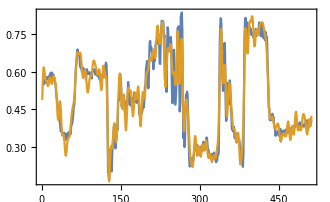

```mathematica
lineChop = InverseFourier[fftChop];
ListLinePlot[{line,lineChop}]
```

As can be seen, the reconstructed data is very similar to the original curve, even though we are only using 1/2 the data.

#### 4. Same thing, but now in 2D

Everything we did above for a single line also applies to the entire image.
It is just not that easy to visualize.

```mathematica
fft = Fourier[imgBW];
ArrayPlot[Abs[fft]^(1/12)]
```

-Graphics-

```mathematica
fftC = Chop[fft,10^-1];
{Times@@Dimensions[fft],Times@@Dimensions[fft]-Count[fftC,0,{2}]}
```

{262144,13428}

The original FT has 262144 nonzero elements. After chopping, we are only left with 13428! 
Or, in terms of kb

```mathematica
IntegerPart[{10^-3. ByteCount[SparseArray[fft]],10^-3. ByteCount[SparseArray[fftC]]}]
```

{6296,786}

The image size is reduced from 6MB to 700kb.

To see if our compression was any good, we compare the original image with the Chopped FT

```mathematica
if = InverseFourier[fftC];
{ArrayPlot[imgBW],ArrayPlot[if]}
```

{-Graphics-,-Graphics-}

Here is the error:

```mathematica
ArrayPlot[Abs[imgBW - if]]
```

-Graphics-

The error is larger in regions with a larger density of details. 
Image compression smears these regions, making the image less crisp.

### Function implementation

```mathematica
ImageBW[img_]:=N@Map[255-Mean[#]&,255 ImageData[img],{2}]

CompressImage[IMG_,imsize_:300]:=Manipulate[
Module[{cf,if},
cf = Chop[fimg,10^Chop[c]];
if = InverseFourier[cf];
Grid[{{
Text@Row[{Style["original (","Label"],IntegerPart[Times@@Dimensions[IMGBW]/10^3.]," kb)"}],Text@Row[{
Style["compressed (","Label"],
IntegerPart[((Times@@Dimensions[IMGBW])-Count[cf,0,{2}])/10^3.],
" kb; ",
IntegerPart[100.((Times@@Dimensions[IMGBW])-Count[cf,0,{2}])/(Times@@Dimensions[IMGBW])],
"% of original size)"

}]
},
{plot,ArrayPlot[if,ImageSize->imsize,PlotRangePadding->None,Frame->False]},
{Text@Style["error","Label"],Text@Style["Power spectrum","Label"]},
{ArrayPlot[Abs[IMGBW - if],ImageSize->imsize,PlotRangePadding->None,Frame->False],ArrayPlot[RotateRight[Sqrt[Sqrt[Abs[cf]]],{128,128}],ImageSize->imsize,PlotRangePadding->None,Frame->False]}}]
],
{{c,1,"compression"},-3,3,.1},Initialization:>{
IMGBW = ImageBW[IMG];
plot :=ArrayPlot[IMGBW,ImageSize->imsize,PlotRangePadding->None,Frame->False];
fimg:=Fourier[N[IMGBW]];
},SynchronousInitialization->False]
```

The function “CompressImage[img]” creates a Manipulate object that allows you to play with different compression ratios.
The function also has the image size as an optional argument: CompressImage[img, imgsize].

### Example gallery (include your own fun pics!)

Tip: don’t leave too many “Manipulate” objects open at the same time. 
It makes the notebook very heavy.

#### Example 1

```mathematica
img=ExampleData[{"TestImage","Lena"}]
```

-Graphics-

```mathematica
(* Click me! *)
CompressImage[img]
```

#### Example 2

```mathematica
CompressImage[-Graphics-]
```

#### Example 3

```mathematica
CompressImage[-Graphics-,500]
```